# Figures 1 and 6

## Charlie Brummitt

This notebook creates figures 1 and 6 of the paper.

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### interpret country names

```mathematica
interpretCountry[name_String]:=Entity["Country",
StringReplace[name,Whitespace->""]/.

{"BosniaandHerzegovina"->"BosniaHerzegovina","Egypt,ArabRep."->"Egypt","SyrianArabRepublic"->"Syria","Yemen,Rep."->"Yemen","Venezuela,R.B."|"Venezuela,RB"|"Venezuela(BolivarianRepublicof)"->"Venezuela","Côted&apos;Ivoire"|"CÃ.b4te d'Ivoire"|"Coted'Ivoire"|"CÃ.b4ted'Ivoire"|"Côted'Ivoire"->"IvoryCoast","Congo,Dem.Rep."|"DemocraticRepublicoftheCongo"->"DemocraticRepublicCongo","Congo"|"Congo,Rep."->"RepublicCongo","KyrgyzRepublic"->"Kyrgyzstan","LaoPDR"|"LaoPeople'sDemocraticRepublic"->"Laos","Macedonia,FYR"->"Macedonia","Gambia,The"->"Gambia","Guinea-Bissau"->"GuineaBissau","RussianFederation"->"Russia","TrinidadandTobago"->"TrinidadTobago","Korea,Rep."|"RepublicofKorea"|"Korea,Republicof"->"SouthKorea","SlovakRepublic"->"Slovakia","WestBankandGaza"->"WestBank","Bahamas,The"->"Bahamas","Micronesia,Fed.Sts."|"Micronesia(FederatedStatesof)"->"Micronesia","Guyana,CR"->"Guyana","Timor-Leste"->"EastTimor","AntiguaandBarbuda"->"AntiguaBarbuda","St.KittsandNevis"->"SaintKittsNevis","St.Lucia"->"SaintLucia","St.VincentandtheGrenadines"->"SaintVincentGrenadines","CaboVerde"->"CapeVerde","VietNam"|"Viet Nam"->"Vietnam","USA"->"UnitedStates","BruneiDarussalam"->"Brunei","TheBahamas"->"Bahamas","SaoTomeandPrincipe"->"SaoTomePrincipe","Iran,IslamicRep."|"Iran(IslamicRepublicof)"->"Iran","MacaoSAR,China"->"Macau","Korea,Dem.Rep."|"DemocraticPeople'sRepublicofKorea"->"NorthKorea","SintMaarten(Dutchpart)"->"SintMaarten","VirginIslands(U.S.)"->"UnitedStatesVirginIslands","TurksandCaicosIslands"->"TurksCaicosIslands","IsleofMan"->"IsleOfMan","FaeroeIslands"->"FaroeIslands","Bolivia(PlurinationalStateof)"->"Bolivia","UnitedStatesofAmerica"->"UnitedStates","UnitedRepublicofTanzania"->"Tanzania","TheformerYugoslavrepublicofMacedonia"|"T.f.Yugo.Rep.ofMacedonia"->"Macedonia","SaintVincentandtheGrenadines"->"SaintVincentGrenadines","SaintKittsandNevis"->"SaintKittsNevis","RepublicofMoldova"->"Moldova","UnitedKingdomofGreatBritainandNorthernIreland"->"UnitedKingdom","HongKongSAR,China"->"HongKong","LibyanArabJamahiriya"->"Libya"}]
```

Figure 1

## Infrastructure data

### import and clean the infrastructure data

```mathematica
infrastructureCopiedXLSsemantic=SemanticImport[FileNameJoin[{NotebookDirectory[],"empirical_data","Infrastructure_allcountries_copied.xlsx"}]];
```

#### clean the infrastructure data

For each country with multiple data points (multiple rows), take the most recent year and discard the other years:

```mathematica
infrastructureDataWithoutDuplicates=infrastructureCopiedXLSsemantic[Select[Head[#Economy]=!=Missing&]][Reverse][DeleteDuplicatesBy["Economy"]][Reverse];
```

#### columns to use

```mathematica
originalColumnHeadings=Normal[infrastructureDataWithoutDuplicates[1,Keys]];
```

Remove spaces and delete */, from the strings:

```mathematica
columnHeadingsToUse=StringJoin/@Map[
(ToUpperCase[StringTake[#,1]]<>StringTake[#,{2,-1}]&),
Map[
ToLowerCase[StringDelete[#,"*"|"/"|","]]&,
StringSplit[First[StringSplit[#,"("]],Whitespace]&/@
Normal[infrastructureDataWithoutDuplicates[1,Keys]],
{2}],
{2}];
```

```mathematica
infrastructureData=infrastructureDataWithoutDuplicates[All,
<|Thread[ReplacePart[columnHeadingsToUse,2->"YearInfrastructureData"]->originalColumnHeadings]
|>][All,Drop[#,{3,5}]&];
```

#### export the data

```mathematica
infrastructureData>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","infrastructureData"}];
```

#### import the data

```mathematica
infrastructureData=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","infrastructureData"}]));
```

## Trade data

#### import the data

```mathematica
FileExistsQ[FileNameJoin[{NotebookDirectory[],"empirical_data","Trade_copied.xlsx"}]]
```

True

```mathematica
tradeSemanticImport=SemanticImport[FileNameJoin[{NotebookDirectory[],"empirical_data","Trade_copied.xlsx"}]];
```

#### clean the data

We will interpret the country names, create a new column for the year, and keep the other columns. 

To keep the other columns, we create an association of those column names:

```mathematica
otherKeysAssoc=(Association[Thread[#->#]]&)@Drop[Normal[tradeSemanticImport[1,Keys]],1];
```

The first 9 rows are for regions, not countries:

```mathematica
tradeSemanticImport[1;;9,"Economy"]//Normal
```

{All Countries,East Asia & Pacific,Eastern Europe & Central Asia,High income nonOECD,High income: OECD,Latin America & Caribbean,Middle East & North Africa,South Asia,Sub-Saharan Africa}

So we drop the first 9 rows, interpret the country name, and rename the year column to “Trade Data Year”:

```mathematica
tradeDataCountries=Dataset[MapThread[Join,Normal/@{
tradeSemanticImport[10;;-1,<|"Economy"->interpretCountry[First@StringSplit[#Economy,"("|")"]],"Trade Data Year"->DateObject[Last[StringSplit[#Economy,"("|")"]]]|>&]
,
tradeSemanticImport[10;;-1,otherKeysAssoc]
}]];
```

#### rename the columns

Now we remove spaces, “*”, and “/” from the column names:

```mathematica
columnHeadings=Normal[tradeDataCountries[1,Keys]];
```

```mathematica
columnHeadingsForComputations=StringJoin/@Map[
(ToUpperCase[StringTake[#,1]]<>StringTake[#,{2,-1}]&),
Map[
ToLowerCase[StringDelete[#,"*"|"/"]]&,
StringSplit[First[StringSplit[#,"("]],Whitespace]&/@
Normal[tradeDataCountries[1,Keys]],
{2}],
{2}];
```

```mathematica
tradeData=tradeDataCountries[All,<|Thread[columnHeadingsForComputations->columnHeadings]|>];
```

#### export the cleaned data

```mathematica
tradeData>>(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","tradeData"}]);
```

#### import the cleaned data

```mathematica
tradeData=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","tradeData"}]));
```

```mathematica
tradeData
```

Dataset[<>]

## Natural disaster risk

### source: WorldRiskReport 2015 (www.worldriskreport.org)

The data we are using is the WorldRiskIndex calculated by United Nations University. It was copied from pages 64–66 of the 2015 report, which has a table of countries and their 
- WorldRiskIndex 
- Exposition 
- Vulnerability 
- Susceptibility 
- Lack of coping capacities
- Lack of adaptive capacities

This data corresponds to year 2015. It was downloaded on February 11, 2016.
We are interested in the data WorldRiskIndex, which combines the other indices. 

Note that year 2013 data is reproduced in the following article on Wikipedia: https://en.wikipedia.org/wiki/List_of_countries _by _natural _disaster _risk

### raw data

I removed spaces from the column names in the table:

```mathematica
columnsWorldRiskIndex={"Rank","Country","WorldRiskIndex", "Exposition","Vulnerability","Susceptibility","LackOfCopingCapacities","LackOfAdaptiveCapacities"};
```

The following was copied from pages 64–66 of the report

```mathematica
rawDataWorldRiskIndex="1. Vanuatu 36.50 % 63.66 % 57.34 % 36.40 % 81.16 % 54.45 %
2. Philippines 28.25 % 52.46 % 53.85 % 33.35 % 80.03 % 48.17 %
3. Tonga 28.23 % 55.27 % 51.08 % 29.15 % 81.80 % 42.28 %
4. Guatemala 20.68 % 36.30 % 56.98 % 37.92 % 80.84 % 52.19 %
5. Bangladesh 19.37 % 31.70 % 61.10 % 40.28 % 86.05 % 56.96 %
6. Solomon Islands 19.18 % 29.98 % 63.98 % 45.37 % 85.44 % 61.12 %
7. Costa Rica 17.33 % 42.61 % 40.68 % 22.98 % 64.61 % 34.46 %
8. El Salvador 17.12 % 32.60 % 52.52 % 32.10 % 75.35 % 50.13 %
9. Cambodia 17.12 % 27.65 % 61.90 % 41.99 % 86.96 % 56.74 %
10. Papua New Guinea 16.74 % 24.94 % 67.15 % 56.06 % 84.22 % 61.16 %
11. Timor-Leste 16.41 % 25.73 % 63.76 % 54.16 % 81.10 % 56.02 %
12. Brunei Darussalam 16.23 % 41.10 % 39.48 % 17.97 % 63.08 % 37.40 %
13. Nicaragua 14.87 % 27.23 % 54.63 % 37.79 % 81.70 % 44.41 %
14. Mauritius 14.78 % 37.35 % 39.56 % 18.94 % 61.68 % 38.07 %
15. Guinea-Bissau 13.75 % 19.65 % 69.94 % 53.21 % 89.71 % 66.90 %
16. Fiji 13.65 % 27.71 % 49.28 % 25.33 % 75.43 % 47.08 %
17. Japan 13.38 % 45.91 % 29.14 % 17.55 % 38.28 % 31.58 %
18. Viet Nam 13.09 % 25.35 % 51.64 % 27.98 % 76.87 % 50.05 %
19. Gambia 12.23 % 19.29 % 63.39 % 46.54 % 83.19 % 60.45 %
20. Jamaica 12.20 % 25.82 % 47.27 % 27.07 % 72.17 % 42.57 %
21. Haiti 12.00 % 16.26 % 73.79 % 62.24 % 91.04 % 68.08 %
22. Guyana 11.81 % 22.90 % 51.56 % 29.02 % 79.47 % 46.18 %
23. Dominican Republic 11.50 % 23.14 % 49.69 % 29.75 % 74.44 % 44.89 %
24. Niger 11.45 % 15.87 % 72.12 % 61.03 % 86.79 % 68.54 %
25. Benin 11.42 % 17.06 % 66.89 % 52.91 % 82.07 % 65.71 %
26. Chile 11.30 % 30.95 % 36.53 % 20.22 % 58.54 % 30.82 %
27. Chad 11.28 % 14.89 % 75.72 % 64.19 % 91.88 % 71.08 %
28. Cameroon 11.20 % 18.19 % 61.59 % 43.57 % 85.27 % 55.92 %
29. Madagascar 11.20 % 16.03 % 69.86 % 65.81 % 83.63 % 60.14 %
30. Senegal 10.96 % 17.57 % 62.40 % 47.42 % 80.53 % 59.26 %
31. Honduras 10.80 % 20.01 % 53.99 % 35.23 % 82.14 % 44.61 %
32. Burundi 10.59 % 15.13 % 70.00 % 63.79 % 87.62 % 58.60 %
33. Sierra Leone 10.57 % 14.65 % 72.10 % 58.33 % 86.11 % 71.84 %
34. Indonesia 10.55 % 19.36 % 54.48 % 32.06 % 80.98 % 50.40 %
35. Togo 10.47 % 15.56 % 67.31 % 54.37 % 85.28 % 62.27 %
36. Cape Verde 10.32 % 20.26 % 50.95 % 34.45 % 70.24 % 48.17 %
37. Albania 10.17 % 21.25 % 47.87 % 21.65 % 74.75 % 47.23 %
38. Zimbabwe 10.01 % 14.96 % 66.92 % 57.27 % 89.19 % 54.30 %
39. Djibouti 9.93 % 16.34 % 60.75 % 37.36 % 82.09 % 62.80 %
40. Afghanistan 9.71 % 13.17 % 73.73 % 55.93 % 93.37 % 71.89 %
41. Burkina Faso 9.62 % 14.32 % 67.17 % 55.39 % 84.06 % 62.05 %
42. Cote d'Ivoire 9.29 % 13.67 % 67.95 % 48.44 % 87.56 % 67.84 %
43. Myanmar 9.14 % 14.87 % 61.48 % 37.32 % 87.21 % 59.92 %
44. Mozambique 9.03 % 12.73 % 70.89 % 65.89 % 84.15 % 62.64 %
45. Mali 8.85 % 12.55 % 70.52 % 55.21 % 85.15 % 71.21 %
46. Ghana 8.77 % 14.48 % 60.56 % 45.17 % 77.63 % 58.88 %
47. Uzbekistan 8.67 % 16.18 % 53.61 % 30.79 % 78.42 % 51.62 %
48. Guinea 8.53 % 12.03 % 70.94 % 54.04 % 89.29 % 69.51 %
49. Suriname 8.42 % 18.12 % 46.48 % 28.21 % 70.96 % 40.27 %
50. Kyrgyzstan 8.33 % 16.63 % 50.10 % 27.35 % 77.09 % 45.87 %
51. Netherlands 8.25 % 30.57 % 26.98 % 14.84 % 42.15 % 23.96 %
52. Nigeria 8.24 % 12.06 % 68.33 % 54.63 % 88.06 % 62.29 %
53. Malawi 8.21 % 12.34 % 66.53 % 60.68 % 83.14 % 55.78 %
54. Mauritania 8.17 % 12.47 % 65.51 % 49.35 % 85.95 % 61.23 %
55. United Republic of Tanzania 8.11 % 12.01 % 67.51 % 64.27 % 83.23 % 55.03 %
56. Sudan 8.08 % 11.86 % 68.15 % 52.44 % 93.05 % 58.96 %
57. Liberia 7.90 % 10.96 % 72.03 % 63.36 % 84.60 % 68.11 %
58. Bhutan 7.83 % 14.81 % 52.86 % 30.74 % 74.80 % 53.03 %
59. Swaziland 7.66 % 12.76 % 60.03 % 46.75 % 80.78 % 52.55 %
60. Algeria 7.63 % 15.82 % 48.24 % 22.93 % 77.02 % 44.76 %
61. Ecuador 7.63 % 16.15 % 47.23 % 29.83 % 73.76 % 38.09 %
62. Zambia 7.61 % 11.37 % 66.95 % 62.78 % 80.30 % 57.76 %
63. Ethiopia 7.57 % 11.12 % 68.12 % 57.73 % 80.24 % 66.38 %
64. Congo 7.53 % 11.65 % 64.66 % 55.69 % 86.16 % 52.11 %
65. Trinidad and Tobago 7.49 % 17.54 % 42.74 % 19.66 % 68.76 % 39.80 %
66. Comoros 7.44 % 10.97 % 67.82 % 59.09 % 84.13 % 60.23 %
67. Sri Lanka 7.43 % 14.79 % 50.26 % 25.65 % 78.52 % 46.60 %
68. Panama 7.41 % 16.45 % 45.03 % 27.92 % 67.87 % 39.30 %
69. Rwanda 7.30 % 11.98 % 60.90 % 54.57 % 79.15 % 48.99 %
70. Tajikistan 7.17 % 12.98 % 55.22 % 34.76 % 76.82 % 54.08 %
71. Greece 7.10 % 21.11 % 33.62 % 17.76 % 51.21 % 31.89 %
72. Pakistan 7.07 % 11.36 % 62.24 % 36.89 % 86.71 % 63.14 %
73. India 7.04 % 11.94 % 58.91 % 38.72 % 80.31 % 57.71 %
74. Lesotho 7.03 % 11.40 % 61.65 % 49.66 % 78.50 % 56.80 %
75. Kenya 7.00 % 10.69 % 65.54 % 55.32 % 85.62 % 55.68 %
76. Serbia 6.91 % 18.05 % 38.30 % 18.47 % 66.17 % 30.27 %
77. Peru 6.91 % 14.40 % 48.00 % 29.57 % 73.28 % 41.16 %
78. China 6.90 % 14.43 % 47.79 % 27.57 % 70.03 % 45.77 %
79. Colombia 6.83 % 13.84 % 49.34 % 28.82 % 75.11 % 44.07 %
80. Morocco 6.80 % 13.25 % 51.34 % 27.92 % 75.71 % 50.40 %
81. Georgia 6.80 % 14.69 % 46.30 % 28.19 % 64.81 % 45.91 %
82. Central African Republic 6.78 % 9.39 % 72.22 % 61.54 % 89.14 % 65.99 %
83. Turkmenistan 6.76 % 13.19 % 51.24 % 27.83 % 75.68 % 50.21 %
84. Uganda 6.69 % 10.16 % 65.90 % 56.05 % 87.68 % 53.95 %
85. Angola 6.67 % 10.18 % 65.51 % 50.26 % 84.89 % 61.37 %
86. Belize 6.59 % 13.31 % 49.52 % 28.18 % 74.23 % 46.14 %
87. Romania 6.55 % 15.77 % 41.52 % 22.12 % 61.36 % 41.08 %
88. Malaysia 6.51 % 14.60 % 44.60 % 19.65 % 67.56 % 46.59 %
89. Cuba 6.42 % 17.45 % 36.79 % 19.62 % 57.20 % 33.56 %
90. Thailand 6.38 % 13.70 % 46.61 % 19.87 % 75.46 % 44.50 %
91. Mexico 6.27 % 13.84 % 45.27 % 23.99 % 72.16 % 39.65 %
92. Gabon 6.26 % 11.95 % 52.41 % 33.51 % 74.53 % 49.18 %
93. Eritrea 6.26 % 8.55 % 73.18 % 61.70 % 88.67 % 69.18 %
94. Armenia 6.21 % 14.51 % 42.78 % 21.24 % 71.09 % 36.02 %
95. Bosnia and Herzegovina 6.20 % 14.02 % 44.26 % 20.63 % 69.64 % 42.51 %
96. T. f. Yugo. Rep. of Macedonia 6.14 % 14.38 % 42.70 % 20.88 % 64.38 % 42.83 %
97. Yemen 6.07 % 9.04 % 67.18 % 45.77 % 91.03 % 64.74 %
98. Azerbaijan 6.04 % 13.16 % 45.90 % 22.39 % 70.36 % 44.96 %
99. Venezuela 5.85 % 13.15 % 44.48 % 23.64 % 74.24 % 35.56 %
100. Lao People's Democratic Republic 5.75 % 9.55 % 60.21 % 41.69 % 84.00 % 54.96 %
101. Namibia 5.61 % 10.41 % 53.92 % 45.70 % 71.02 % 45.04 %
102. Syrian Arab Republic 5.58 % 10.56 % 52.82 % 26.28 % 84.38 % 47.82 %
103. Tunisia 5.47 % 12.45 % 43.96 % 21.02 % 72.51 % 38.36 %
104. Hungary 5.46 % 15.61 % 34.96 % 16.76 % 53.27 % 34.86 %
105. Botswana 5.45 % 10.55 % 51.62 % 37.03 % 67.31 % 50.52 %
106. South Africa 5.38 % 12.08 % 44.55 % 30.38 % 69.58 % 33.69 %
107. Turkey 5.34 % 12.25 % 43.59 % 20.54 % 67.57 % 42.67 %
108. Nepal 5.29 % 9.16 % 57.73 % 42.42 % 80.38 % 50.40 %
109. Bolivia 5.04 % 8.98 % 56.14 % 40.91 % 80.19 % 47.33 %
110. Lebanon 5.01 % 11.14 % 44.94 % 20.21 % 70.00 % 44.61 %
111. Republic of Moldova 4.92 % 11.11 % 44.31 % 22.92 % 68.06 % 41.94 %
112. Iran 4.88 % 10.19 % 47.92 % 20.05 % 81.58 % 42.13 %
113. Iraq 4.84 % 8.08 % 59.82 % 30.06 % 89.30 % 60.10 %
114. Korea, Republic of 4.80 % 14.89 % 32.26 % 15.02 % 46.60 % 35.14 %
115. Jordan 4.75 % 10.53 % 45.09 % 22.03 % 68.79 % 44.44 %
116. Equatorial Guinea 4.71 % 8.22 % 57.28 % 30.19 % 85.09 % 56.58 %
117. Ireland 4.52 % 14.74 % 30.64 % 16.05 % 46.57 % 29.31 %
118. Italy 4.48 % 13.85 % 32.36 % 17.27 % 54.41 % 25.39 %
119. Brazil 4.30 % 9.53 % 45.09 % 25.53 % 66.60 % 43.15 %
120. Croatia 4.28 % 11.53 % 37.13 % 18.18 % 55.97 % 37.24 %
121. Bulgaria 4.21 % 11.66 % 36.08 % 17.57 % 56.56 % 34.10 %
122. New Zealand 4.20 % 15.44 % 27.22 % 16.74 % 43.79 % 21.13 %
123. Bahamas 4.19 % 10.71 % 39.09 % 19.06 % 53.43 % 44.80 %
124. Uruguay 4.00 % 11.10 % 36.05 % 21.56 % 50.80 % 35.78 %
125. Libyan Arab Jamahiriya 4.00 % 7.80 % 51.27 % 26.16 % 76.53 % 51.10 %
126. Australia 3.93 % 15.05 % 26.10 % 15.05 % 42.29 % 20.96 %
127. United States 3.88 % 12.25 % 31.67 % 16.47 % 48.57 % 29.98 %
128. Russia 3.85 % 9.38 % 41.05 % 21.59 % 58.80 % 42.76 %
129. Kazakhstan 3.74 % 9.11 % 41.09 % 18.00 % 63.57 % 41.72 %
130. Paraguay 3.74 % 7.03 % 53.18 % 32.32 % 79.12 % 48.10 %
131. Argentina 3.68 % 9.55 % 38.55 % 21.04 % 59.72 % 34.90 %
132. Slovenia 3.64 % 11.59 % 31.42 % 16.02 % 51.15 % 27.08 %
133. Portugal 3.61 % 10.93 % 33.01 % 17.91 % 48.38 % 32.73 %
134. Austria 3.58 % 13.60 % 26.31 % 14.36 % 37.61 % 26.95 %
135. Slovakia 3.57 % 10.21 % 34.92 % 14.53 % 55.66 % 34.57 %
136. United Kingdom 3.54 % 11.60 % 30.49 % 16.57 % 47.08 % 27.82 %
137. Czech Republic 3.46 % 10.82 % 32.02 % 15.07 % 50.87 % 30.12 %
138. Latvia 3.45 % 9.26 % 37.30 % 21.12 % 55.19 % 35.57 %
139. Belgium 3.41 % 11.66 % 29.23 % 15.59 % 42.38 % 29.70 %
140. Kuwait 3.34 % 9.04 % 36.98 % 11.53 % 66.24 % 33.17 %
141. Poland 3.28 % 9.79 % 33.51 % 17.67 % 53.16 % 29.68 %
142. Spain 3.20 % 10.23 % 31.27 % 16.08 % 52.00 % 25.74 %
143. Canada 3.14 % 10.25 % 30.61 % 15.19 % 46.45 % 30.19 %
144. Belarus 3.12 % 8.46 % 36.89 % 16.87 % 61.69 % 32.12 %
145. Ukraine 3.11 % 7.50 % 41.42 % 19.10 % 61.15 % 44.02 %
146. Lithuania 3.01 % 8.88 % 33.91 % 18.58 % 49.36 % 33.78 %
147. Germany 3.01 % 11.41 % 26.37 % 15.41 % 37.73 % 25.97 %
148. Mongolia 3.00 % 6.52 % 46.07 % 31.05 % 64.67 % 42.47 %
149. Denmark 2.93 % 10.87 % 27.00 % 15.08 % 39.49 % 26.42 %
150. Cyprus 2.76 % 7.44 % 37.13 % 14.85 % 58.05 % 38.48 %
151. Oman 2.74 % 6.41 % 42.75 % 15.98 % 63.51 % 48.76 %
152. France 2.69 % 9.25 % 29.08 % 16.13 % 43.29 % 27.83 %
153. Luxembourg 2.52 % 9.12 % 27.66 % 12.87 % 41.44 % 28.67 %
154. Seychelles 2.51 % 5.99 % 41.86 % 22.44 % 63.20 % 39.93 %
155. Switzerland 2.48 % 9.56 % 25.98 % 14.93 % 37.92 % 25.10 %
156. Estonia 2.43 % 7.23 % 33.57 % 18.67 % 51.15 % 30.89 %
157. Israel 2.38 % 6.41 % 37.20 % 19.15 % 58.93 % 33.52 %
158. Norway 2.31 % 8.58 % 26.86 % 14.41 % 40.05 % 26.13 %
159. Egypt 2.29 % 4.72 % 48.56 % 21.34 % 77.86 % 46.48 %
160. Singapore 2.25 % 7.82 % 28.78 % 14.41 % 49.20 % 22.73 %
161. Finland 2.24 % 8.19 % 27.38 % 15.60 % 39.39 % 27.17 %
162. Sweden 2.19 % 7.97 % 27.49 % 15.39 % 40.90 % 26.18 %
163. United Arab Emirates 1.91 % 5.93 % 32.27 % 10.47 % 56.51 % 29.84 %
164. Bahrain 1.78 % 4.27 % 41.56 % 13.04 % 66.57 % 45.07 %
165. Kiribati 1.72 % 3.05 % 56.45 % 42.31 % 83.69 % 43.36 %
166. Iceland 1.56 % 5.67 % 27.46 % 15.00 % 43.15 % 24.21 %
167. Grenada 1.44 % 3.13 % 46.15 % 24.99 % 69.03 % 44.43 %
168. Barbados 1.21 % 3.46 % 34.95 % 16.85 % 50.36 % 37.63 %
169. Saudi Arabia 1.17 % 2.93 % 39.82 % 15.19 % 70.05 % 34.22 %
170. Malta 0.62 % 1.65 % 37.67 % 15.28 % 59.58 % 38.16 %
171. Qatar 0.08 % 0.28 % 30.30 % 8.97 % 44.76 % 37.16 %";
```

### clean and parse the data

#### parse each row

This is what one row looks like:

```mathematica
StringSplit[rawDataWorldRiskIndex,"\n"][[1]]
```

1. Vanuatu 36.50 % 63.66 % 57.34 % 36.40 % 81.16 % 54.45 %

The function parseRow converts this to a list of interpreted values:

```mathematica
parseRow[row_]:=Module[{positionSpaceAfterRank,positionSpaceBeforeFirstPercentageValue},
positionSpaceAfterRank=StringPosition[row,RegularExpression["\\d+. "]]⟦1,2⟧;
positionSpaceBeforeFirstPercentageValue=StringPosition[row,RegularExpression[" [\\d.%]+ "]]⟦1,1⟧;

Join[<|
"Rank"->StringTake[row,{1,positionSpaceAfterRank-2}],
"Economy"-> interpretCountry[StringTake[row,{positionSpaceAfterRank+1,positionSpaceBeforeFirstPercentageValue-1}]]
|>,
AssociationThread[
Drop[columnsWorldRiskIndex,2]->
(ToExpression[StringDrop[#,-1]]/100&/@StringSplit[StringTake[row,{positionSpaceBeforeFirstPercentageValue+1,-1}]," "])
]
]
]
```

#### parse all rows to form a Dataset

```mathematica
worldRiskDataset=Dataset[parseRow/@StringSplit[
StringReplace[rawDataWorldRiskIndex," %"->"%"]
,"\n"]];
```

#### export the cleaned dataset

```mathematica
worldRiskDataset>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","worldRiskDataset"}];
```

#### import the cleaned dataset

```mathematica
worldRiskDataset=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","worldRiskDataset"}]));
```

## Crime data from the Enterprise Survey

### import crime.xls

```mathematica
FileExistsQ[FileNameJoin[{"empirical_data","Crime_copied.xlsx"}]]
```

True

```mathematica
crimeRawData=SemanticImport[FileNameJoin[{"empirical_data","Crime_copied.xlsx"}]]
```

Dataset[<>]

Again, the first 9 rows are for regions rather than countries:

```mathematica
crimeRawData[1;;9,"Economy"]
```

Dataset[<>]

So we drop the first 9 rows and interpret the country names:

```mathematica
crimeCountries=Normal[interpretCountry[StringDrop[#,-7]]&/@crimeRawData[10;;,1]]
```

{Afghanistan,Albania,Algeria,Angola,Antigua and Barbuda,Argentina,Armenia,Azerbaijan,Bahamas,Bangladesh,Barbados,Belarus,Belize,Benin,Bhutan,Bolivia,Bosnia and Herzegovina,Botswana,Brazil,Bulgaria,Burkina Faso,Burundi,Cape Verde,Cambodia,Cameroon,Central African Republic,Chad,Chile,China,Colombia,Democratic Republic of the Congo,Republic of the Congo,Costa Rica,Ivory Coast,Croatia,Czech Republic,Djibouti,Dominica,Dominican Republic,Ecuador,Egypt,El Salvador,Eritrea,Estonia,Ethiopia,Fiji,Gabon,Gambia,Georgia,Germany,Ghana,Greece,Grenada,Guatemala,Guinea,Guinea-Bissau,Guyana,Honduras,Hungary,India,Indonesia,Iraq,Ireland,Israel,Jamaica,Jordan,Kazakhstan,Kenya,South Korea,Kosovo,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Mali,Mauritania,Mauritius,Mexico,Micronesia,Moldova,Mongolia,Montenegro,Morocco,Mozambique,Myanmar,Namibia,Nepal,Nicaragua,Niger,Nigeria,Pakistan,Panama,Paraguay,Peru,Philippines,Poland,Portugal,Romania,Russia,Rwanda,Samoa,Senegal,Serbia,Sierra Leone,Slovakia,Slovenia,South Africa,South Sudan,Spain,Sri Lanka,Saint Kitts and Nevis,Saint Lucia,Saint Vincent and the Grenadines,Sudan,Suriname,Swaziland,Sweden,Syria,Tajikistan,Tanzania,Thailand,East Timor,Togo,Tonga,Trinidad and Tobago,Tunisia,Turkey,Uganda,Ukraine,Uruguay,Uzbekistan,Vanuatu,Venezuela,Vietnam,West Bank,Yemen,Zambia,Zimbabwe}

Remove spaces and non-letter characters from the column headings:

```mathematica
crimeHeadings=StringJoin/@Map[
(ToUpperCase[StringTake[#,1]]<>StringTake[#,{2,-1}]&),
Map[
ToLowerCase[StringDelete[#,"*"|"/"|","]]&,
StringSplit[First[StringSplit[#,"("]],Whitespace]&/@
Normal[crimeRawData[1,Keys]],
{2}],
{2}]
```

{Economy,PercentOfFirmsPayingForSecurity,SecurityCosts,IfTheEstablishmentPaysForSecurityAverageSecurityCosts,PercentOfFirmsExperiencingLossesDueToTheftAndVandalism,LossesDueToTheftAndVandalismAgainstTheFirm,IfThereWereLossesAverageLossesDueToTheftAndVandalism,ProductsShippedToSupplyDomesticMarketsThatWereLostDueToTheft,PercentOfFirmsIdentifyingCrimeTheftAndDisorderAsAMajorConstraint}

```mathematica
crimeDataset=Dataset[AssociationThread[crimeHeadings->#]&/@(Join@@#&/@Transpose[{List/@crimeCountries,Values/@Normal@crimeRawData[10;;,2;;]}])]
```

Dataset[<>]

#### export the crime data

```mathematica
crimeDataset>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","crimeDataset"}];
```

#### import the crime data

```mathematica
crimeDataset=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","crimeDataset"}]));
```

## GDP per capita in current USD and current international dollars PPP from the World Bank

### source of the data

Two files were downloaded February 15, 2016 from the world bank website: 
1. GDP per capita (current US$) was downloaded from http://data.worldbank.org/indicator/NY.GDP.PCAP.CD
	File Name: GDP per capita in current USD from the World Bank.xls
	
2. GDP per capita (PPP ) was downloaded from http://data.worldbank.org/indicator/NY.GDP.PCAP.PP.CD
	File Name: GDP per capita PPP in current international dollars.xls

### current USD data

#### import raw data

```mathematica
FileExistsQ[FileNameJoin[{NotebookDirectory[],"empirical_data","GDP per capita in current USD from the World Bank.xls"}]]
```

True

```mathematica
gdpPerCapitaWorldBankRaw=Import[FileNameJoin[{NotebookDirectory[],"empirical_data","GDP per capita in current USD from the World Bank.xls"}]];
```

#### process the data

Column names:

```mathematica
gdpPerCapitaWorldBankRaw[[1,4]]
```

{Country Name,Country Code,Indicator Name,Indicator Code,1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015}

These are the column names that are years:

```mathematica
gdpPerCapitaWorldBankYears=gdpPerCapitaWorldBankRaw[[1,4,5;;]]
```

{1960,1961,1962,1963,1964,1965,1966,1967,1968,1969,1970,1971,1972,1973,1974,1975,1976,1977,1978,1979,1980,1981,1982,1983,1984,1985,1986,1987,1988,1989,1990,1991,1992,1993,1994,1995,1996,1997,1998,1999,2000,2001,2002,2003,2004,2005,2006,2007,2008,2009,2010,2011,2012,2013,2014,2015}

Many of the rows correspond to regions or groups of countries:

```mathematica
MapIndexed[{#2[[1]],interpretCountry[#1]}&,gdpPerCapitaWorldBankRaw[[1,5;;,1]]]
```

{{1,Aruba},{2,Andorra},{3,Afghanistan},{4,Angola},{5,Albania},{6,Entity[Country,ArabWorld]},{7,United Arab Emirates},{8,Argentina},{9,Armenia},{10,American Samoa},{11,Antigua and Barbuda},{12,Australia},{13,Austria},{14,Azerbaijan},{15,Burundi},{16,Belgium},{17,Benin},{18,Burkina Faso},{19,Bangladesh},{20,Bulgaria},{21,Bahrain},{22,Bahamas},{23,Bosnia and Herzegovina},{24,Belarus},{25,Belize},{26,Bermuda},{27,Bolivia},{28,Brazil},{29,Barbados},{30,Brunei},{31,Bhutan},{32,Botswana},{33,Central African Republic},{34,Canada},{35,Entity[Country,CentralEuropeandtheBaltics]},{36,Switzerland},{37,Entity[Country,ChannelIslands]},{38,Chile},{39,China},{40,Ivory Coast},{41,Cameroon},{42,Republic of the Congo},{43,Colombia},{44,Comoros},{45,Cape Verde},{46,Costa Rica},{47,Entity[Country,Caribbeansmallstates]},{48,Cuba},{49,Curacao},{50,Cayman Islands},{51,Cyprus},{52,Czech Republic},{53,Germany},{54,Djibouti},{55,Dominica},{56,Denmark},{57,Dominican Republic},{58,Algeria},{59,Entity[Country,EastAsia&Pacific(developingonly)]},{60,Entity[Country,EastAsia&Pacific(allincomelevels)]},{61,Entity[Country,Europe&CentralAsia(developingonly)]},{62,Entity[Country,Europe&CentralAsia(allincomelevels)]},{63,Ecuador},{64,Egypt},{65,Entity[Country,Euroarea]},{66,Eritrea},{67,Spain},{68,Estonia},{69,Ethiopia},{70,Entity[Country,EuropeanUnion]},{71,Entity[Country,Fragileandconflictaffectedsituations]},{72,Finland},{73,Fiji},{74,France},{75,Faroe Islands},{76,Micronesia},{77,Gabon},{78,United Kingdom},{79,Georgia},{80,Ghana},{81,Guinea},{82,Gambia},{83,Guinea-Bissau},{84,Equatorial Guinea},{85,Greece},{86,Grenada},{87,Greenland},{88,Guatemala},{89,Guam},{90,Guyana},{91,Entity[Country,Highincome]},{92,Hong Kong},{93,Honduras},{94,Entity[Country,Heavilyindebtedpoorcountries(HIPC)]},{95,Croatia},{96,Haiti},{97,Hungary},{98,Indonesia},{99,Isle of Man},{100,India},{101,Entity[Country,Notclassified]},{102,Ireland},{103,Iran},{104,Iraq},{105,Iceland},{106,Israel},{107,Italy},{108,Jamaica},{109,Jordan},{110,Japan},{111,Kazakhstan},{112,Kenya},{113,Kyrgyzstan},{114,Cambodia},{115,Kiribati},{116,Saint Kitts and Nevis},{117,South Korea},{118,Kosovo},{119,Kuwait},{120,Entity[Country,LatinAmerica&Caribbean(developingonly)]},{121,Laos},{122,Lebanon},{123,Liberia},{124,Libya},{125,Saint Lucia},{126,Entity[Country,LatinAmerica&Caribbean(allincomelevels)]},{127,Entity[Country,Leastdevelopedcountries:UNclassification]},{128,Entity[Country,Lowincome]},{129,Liechtenstein},{130,Sri Lanka},{131,Entity[Country,Lowermiddleincome]},{132,Entity[Country,Low&middleincome]},{133,Lesotho},{134,Lithuania},{135,Luxembourg},{136,Latvia},{137,Macau},{138,Entity[Country,St.Martin(Frenchpart)]},{139,Morocco},{140,Monaco},{141,Moldova},{142,Madagascar},{143,Maldives},{144,Entity[Country,MiddleEast&NorthAfrica(allincomelevels)]},{145,Mexico},{146,Marshall Islands},{147,Entity[Country,Middleincome]},{148,Macedonia},{149,Mali},{150,Malta},{151,Myanmar},{152,Entity[Country,MiddleEast&NorthAfrica(developingonly)]},{153,Montenegro},{154,Mongolia},{155,Northern Mariana Islands},{156,Mozambique},{157,Mauritania},{158,Mauritius},{159,Malawi},{160,Malaysia},{161,Entity[Country,NorthAmerica]},{162,Namibia},{163,New Caledonia},{164,Niger},{165,Nigeria},{166,Nicaragua},{167,Netherlands},{168,Entity[Country,Highincome:nonOECD]},{169,Norway},{170,Nepal},{171,New Zealand},{172,Entity[Country,Highincome:OECD]},{173,Entity[Country,OECDmembers]},{174,Oman},{175,Entity[Country,Othersmallstates]},{176,Pakistan},{177,Panama},{178,Peru},{179,Philippines},{180,Palau},{181,Papua New Guinea},{182,Poland},{183,Puerto Rico},{184,North Korea},{185,Portugal},{186,Paraguay},{187,Entity[Country,Pacificislandsmallstates]},{188,French Polynesia},{189,Qatar},{190,Romania},{191,Russia},{192,Rwanda},{193,Entity[Country,SouthAsia]},{194,Saudi Arabia},{195,Sudan},{196,Senegal},{197,Singapore},{198,Solomon Islands},{199,Sierra Leone},{200,El Salvador},{201,San Marino},{202,Somalia},{203,Serbia},{204,Entity[Country,Sub-SaharanAfrica(developingonly)]},{205,South Sudan},{206,Entity[Country,Sub-SaharanAfrica(allincomelevels)]},{207,Entity[Country,Smallstates]},{208,São Tomé and Príncipe},{209,Suriname},{210,Slovakia},{211,Slovenia},{212,Sweden},{213,Swaziland},{214,Sint Maarten},{215,Seychelles},{216,Syria},{217,Turks and Caicos Islands},{218,Chad},{219,Togo},{220,Thailand},{221,Tajikistan},{222,Turkmenistan},{223,East Timor},{224,Tonga},{225,Trinidad and Tobago},{226,Tunisia},{227,Turkey},{228,Tuvalu},{229,Tanzania},{230,Uganda},{231,Ukraine},{232,Entity[Country,Uppermiddleincome]},{233,Uruguay},{234,United States},{235,Uzbekistan},{236,Saint Vincent and the Grenadines},{237,Venezuela},{238,United States Virgin Islands},{239,Vietnam},{240,Vanuatu},{241,West Bank},{242,World},{243,Samoa},{244,Yemen},{245,South Africa},{246,Democratic Republic of the Congo},{247,Zambia},{248,Zimbabwe}}

These are the positions of the rows that correspond to countries as opposed to regions or groups of countries:

```mathematica
gdpPerCapitaWorldBankPositionsOfCountries=SparseArray[{Alternatives[6,35,37,47,59,60,61,62,65,70,71,91,94,101,120,126,127,128,131,132,138,144,147,152,161,168,172,173,175,187,193,204,206,207,232]->0},Length[gdpPerCapitaWorldBankRaw[[1,5;;,1]]],1]//Normal
```

{1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,0,0,0,0,1,1,0,1,1,1,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,0,0,1,1,0,0,1,1,1,1,1,0,1,1,1,1,1,0,1,1,0,1,1,1,1,0,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Now we create time series (TimeSeries) for the GDP data. Because we’re missing GDP data for "Curacao" and "Sint Maarten", we retrieve the 2014 GDP per capita using the built-in knowledge of the Wolfram Language for those two countries:

```mathematica
gdpPerCapitaWorldBankInterpreted=
Dataset[
Module[{country},
country=interpretCountry[First[#]];

<|"Economy"->country,

"GDPperCapitaCurrentUSD"->
(If[#=={},
(* compute the GDP using the built-in knowledge of the WL *)
TimeSeries[{{DateObject[{2014}],TimeConstrained[EntityValue[country,EntityProperty["Country","GDP",{"CurrencyUnit"->"CurrentUSDollar","PerCapita"->"PerCapita","Date"->DateObject[{2014}]}]],10,Missing["NotEnoughTimeToCompute"]]}}]
,
(* else we have data from the World Bank *)
TimeSeries[#]]&@Select[Transpose[{DateObject[{ToExpression@#}]&/@gdpPerCapitaWorldBankYears,If[#=="",Missing["Unknown"],Quantity[#,DatedUnit["USDollars",DateList@gdpPerCapitaWorldBankRaw[[1,2,2]]]]]&/@#[[5;;]]}],Last[#]=!=Missing["Unknown"]&])
|>
]
&/@Take[Pick[gdpPerCapitaWorldBankRaw[[1,5;;]],gdpPerCapitaWorldBankPositionsOfCountries,1],All]
](*[Select[Not[MemberQ[{Entity["Country","Curacao"],Entity["Country","SintMaarten"]},#Economy]]&]]*)
```

Dataset[<>]

Here are the counts of the most recent year available for GDP per capita:

```mathematica
gdpPerCapitaWorldBankInterpreted[Tally,Normal[First[#]][[1]]&@#GDPperCapitaCurrentUSD["DatePath"]⟦-1⟧&]
```

Dataset[<>]

Here’s the data grouped by the most recent year available:

```mathematica
gdpPerCapitaWorldBankInterpreted[1;;-1][GroupBy[Normal[First[#]][[1]]&@#GDPperCapitaCurrentUSD["DatePath"]⟦-1⟧&]]
```

2011 | { <| Economy→Aruba,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_3 }
2013 | { <| Economy→Andorra,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_8 }
2014 | { <| Economy→Afghanistan,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_187 }
2006 | { <| Economy→Cayman Islands,GDPperCapitaCurrentUSD→TimeSeries[…] |> }
2009 | { <| Economy→Greenland,GDPperCapitaCurrentUSD→TimeSeries[…] |> }
2007 | { <| Economy→Isle of Man,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_1 }
2012 | { <| Economy→Liechtenstein,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_1 }
2000 | { <| Economy→New Caledonia,GDPperCapitaCurrentUSD→TimeSeries[…] |>,⋯_1 }
2008 | { <| Economy→San Marino,GDPperCapitaCurrentUSD→TimeSeries[…] |> }
1993 | { <| Economy→United States Virgin Islands,GDPperCapitaCurrentUSD→TimeSeries[…] |> }
3 levels | 10rows | Dataset[_Association]

#### export the data:

```mathematica
gdpPerCapitaWorldBankInterpreted>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","gdpPerCapitaWorldBankInterpreted"}];
```

#### import the processed data

```mathematica
gdpPerCapitaWorldBankInterpreted=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","gdpPerCapitaWorldBankInterpreted"}]));
```

## Economic Complexity Index

### import data

#### import

```mathematica
FileExistsQ@FileNameJoin[{NotebookDirectory[],"empirical_data","ECI_country_rankings.csv"}]
```

True

```mathematica
ECIrawData=Import[FileNameJoin[{NotebookDirectory[],"empirical_data","ECI_country_rankings.csv"}],"Data"];
```

The countries in the ECI dataset:

```mathematica
ECIrawData[[2;;,3]]//Sort//Union
```

{Albania,Algeria,Angola,Argentina,Australia,Austria,Azerbaijan,Bangladesh,Belarus,Belgium,Bolivia,Bosnia and Herzegovina,Botswana,Brazil,Bulgaria,Cambodia,Cameroon,Canada,Chile,China,Colombia,Congo,Costa Rica,Cote d'Ivoire,Croatia,Cuba,Czech Republic,Denmark,Dominican Republic,Ecuador,Egypt,El Salvador,Estonia,Ethiopia,Finland,France,Gabon,Georgia,Germany,Ghana,Greece,Guatemala,Guinea,Honduras,Hong Kong,Hungary,India,Indonesia,Iran,Ireland,Israel,Italy,Jamaica,Japan,Jordan,Kazakhstan,Kenya,Korea, Rep.,Kuwait,Lao PDR,Latvia,Lebanon,Libya,Lithuania,Macedonia,Madagascar,Malawi,Malaysia,Mauritania,Mauritius,Mexico,Moldova,Mongolia,Morocco,Mozambique,Namibia,Netherlands,New Zealand,Nicaragua,Nigeria,Norway,Oman,Pakistan,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Poland,Portugal,Qatar,Romania,Russia,Saudi Arabia,Senegal,Serbia,Singapore,Slovak Republic,Slovenia,South Africa,Spain,Sri Lanka,Sudan,Sweden,Switzerland,Syrian Arab Republic,Tanzania,Thailand,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,Uruguay,Uzbekistan,Venezuela,Viet Nam,Yemen,Zambia,Zimbabwe}

Interpret the countries:

```mathematica
ECIdataset=Dataset[AssociationThread[{"rank","abbrv","Economy","eciValue","delta","year"}->MapAt[interpretCountry,#,3]]&/@Rest[ECIrawData]];
```

#### put the time series in the table entries

```mathematica
ECIdatasetTimeSeries=ECIdataset[1;;-1][GroupBy["Economy"],<|"Economy"->#⟦1,"Economy"⟧,"eciValue"->(TemporalData@(Values/@#⟦All,{"year","eciValue"}⟧)),"deltaECI"->(TemporalData@(Values/@#⟦All,{"year","delta"}⟧)),"rankECI"->(TemporalData@(Values/@#⟦All,{"year","rank"}⟧))|>&][Values];
```

## Cause of death by injury and by communicable disease

### injury

#### import raw data

Downloaded Feb. 9, 2016 from http://data.worldbank.org/indicator/SH.DTH.INJR.ZS

```mathematica
causeOfDeathByInjuryRawData=Import[FileNameJoin[{NotebookDirectory[],"empirical_data","Cause of death, by injury.xls"}]];
```

```mathematica
causeOfDeathByInjuryRawData[[1,1;;5]]//Grid[#,ItemSize->20]&
```

Data Source | World Development Indicators |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Last Updated Date | Tue 22 Dec 2015 00:00:00GMT-7. |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
Country Name | Country Code | Indicator Name | Indicator Code | 1960 | 1961 | 1962 | 1963 | 1964 | 1965 | 1966 | 1967 | 1968 | 1969 | 1970 | 1971 | 1972 | 1973 | 1974 | 1975 | 1976 | 1977 | 1978 | 1979 | 1980 | 1981 | 1982 | 1983 | 1984 | 1985 | 1986 | 1987 | 1988 | 1989 | 1990 | 1991 | 1992 | 1993 | 1994 | 1995 | 1996 | 1997 | 1998 | 1999 | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015
Aruba | ABW | Cause of death, by injury (% of total) | SH.DTH.INJR.ZS |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

Interpret the country names and ignore the regions and groups of countries:

```mathematica
deathsByInjuryDataset=Dataset[Map[<|"Economy"->interpretCountry[#⟦1⟧],"PercentageDeathsByInjury2012"->If[#⟦2⟧=="",Missing["Unknown"],Quantity[#⟦2⟧,"Percent"]]|>&,

Select[causeOfDeathByInjuryRawData[[1,5;;,{1,57}]]
,
Not[MemberQ[Entity["Country",#]&/@{"ArabWorld","CentralEuropeandtheBaltics","ChannelIslands","Caribbeansmallstates","EastAsia&Pacific(developingonly)","EastAsia&Pacific(allincomelevels)","Europe&CentralAsia(developingonly)","Europe&CentralAsia(allincomelevels)","Euroarea","EuropeanUnion","Fragileandconflictaffectedsituations","Highincome","Heavilyindebtedpoorcountries(HIPC)","HongKongSAR,China","Notclassified","LatinAmerica&Caribbean(developingonly)","LatinAmerica&Caribbean(allincomelevels)","Leastdevelopedcountries:UNclassification","Lowermiddleincome","Low&middleincome","St.Martin(Frenchpart)","MiddleEast&NorthAfrica(allincomelevels)","Middleincome","MiddleEast&NorthAfrica(developingonly)","NorthAmerica","Highincome:nonOECD","Highincome:OECD","OECDmembers","Othersmallstates","Pacificislandsmallstates","SouthAsia","Sub-SaharanAfrica(developingonly)","Sub-SaharanAfrica(allincomelevels)","Lowincome","Smallstates","Uppermiddleincome"},interpretCountry@First[#]]]&]

]]
```

Dataset[<>]

#### export the cleaned data

```mathematica
deathsByInjuryDataset>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","deathsByInjuryDataset"}];
```

#### import processed data

```mathematica
deathsByInjuryDataset=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","deathsByInjuryDataset"}]));
```

### deaths by communicable disease

#### import raw data

Downloaded Feb. 15, 2016 from http://data.worldbank.org/indicator/SH.DTH.COMM.ZS

```mathematica
causeOfDeathByCommunicableDiseaseRawData=Import[FileNameJoin[{NotebookDirectory[],"empirical_data","Cause of death by communicable diseases.xls"}]];
```

Interpret country names, ignore regions and groups of countries, and grab the second column (“PercentageDeathsByCommunicableDisease2012”):

```mathematica
deathsByCommunicableDiseaseDataset=Dataset[Map[<|"Economy"->interpretCountry[#⟦1⟧],"PercentageDeathsByCommunicableDisease2012"->If[#⟦2⟧=="",Missing["Unknown"],Quantity[#⟦2⟧,"Percent"]]|>&,

Select[causeOfDeathByCommunicableDiseaseRawData[[1,5;;,{1,57}]]
,
Not[MemberQ[Entity["Country",#]&/@{"ArabWorld","CentralEuropeandtheBaltics","ChannelIslands","Caribbeansmallstates","EastAsia&Pacific(developingonly)","EastAsia&Pacific(allincomelevels)","Europe&CentralAsia(developingonly)","Europe&CentralAsia(allincomelevels)","Euroarea","EuropeanUnion","Fragileandconflictaffectedsituations","Highincome","Heavilyindebtedpoorcountries(HIPC)","HongKongSAR,China","Notclassified","LatinAmerica&Caribbean(developingonly)","LatinAmerica&Caribbean(allincomelevels)","Leastdevelopedcountries:UNclassification","Lowermiddleincome","Low&middleincome","St.Martin(Frenchpart)","MiddleEast&NorthAfrica(allincomelevels)","Middleincome","MiddleEast&NorthAfrica(developingonly)","NorthAmerica","Highincome:nonOECD","Highincome:OECD","OECDmembers","Othersmallstates","Pacificislandsmallstates","SouthAsia","Sub-SaharanAfrica(developingonly)","Sub-SaharanAfrica(allincomelevels)","Lowincome","Smallstates","Uppermiddleincome"},interpretCountry@First[#]]]&]

]]
```

Dataset[<>]

#### export the cleaned data

```mathematica
deathsByCommunicableDiseaseDataset>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","deathsByCommunicableDiseaseDataset"}];
```

#### import processed data

```mathematica
deathsByCommunicableDiseaseDataset=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","deathsByCommunicableDiseaseDataset"}]));
```

### adult mortality rate

#### import raw data

Downloaded Feb. 15, 2016 from the WHO website at http://apps.who.int/gho/data/node.main.11?lang=en

```mathematica
adultMortalityRawData=Import[FileNameJoin[{NotebookDirectory[],"empirical_data","WHO-data-adult-mortality-copied.xlsx"}]];
```

Interpret the country names and convert the mortality rates into probabilities (they’re reported as deaths per 1000 individuals):

```mathematica
adultMortalityDataset=Dataset[<|"Economy"->interpretCountry[First[#]],"AdultMortalityRateBothSexes2013"->(ToExpression[#⟦3⟧]/1000),"AdultMortalityRateFemale2013"->(ToExpression[#⟦4⟧]/1000),"AdultMortalityRateMale2013"->(ToExpression[#⟦5⟧]/1000)|>&/@adultMortalityRawData[[1,3;;-1;;4]]]
```

Dataset[<>]

#### export the cleaned data

```mathematica
adultMortalityDataset>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","adultMortalityDataset"}];
```

#### import processed data

```mathematica
adultMortalityDataset=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","adultMortalityDataset"}]));
```

## Combine the datasets

#### code for joining datasets

Do an outer join to keep all the data that we have:

```mathematica
(* join two datasets *)joinDatasetsOuter[dataset1_,dataset2_,key_]:=Dataset[JoinAcross[Normal[dataset1],Normal[dataset2],key,"Outer"]];

(* join a list of datasets *)
joinDatasetsOuter[datasets_List,key_]:=Fold[joinDatasetsOuter[#1,#2,key]&,datasets[[1]],Rest[datasets]];
```

### combine the datasets

There are very different numbers of countries in the datasets:

```mathematica
Length/@{infrastructureData,tradeDataCountries,ECIdatasetTimeSeries,crimeDataset,worldRiskDataset,gdpPerCapitaWorldBankInterpreted,deathsByInjuryDataset,deathsByCommunicableDiseaseDataset,adultMortalityDataset}
```

{132,144,124,145,171,213,212,212,194}

Combine all the datasets:

```mathematica
combinedDatasets=joinDatasetsOuter[{infrastructureData,tradeData,ECIdatasetTimeSeries,crimeDataset,worldRiskDataset,gdpPerCapitaWorldBankInterpreted,deathsByInjuryDataset,deathsByCommunicableDiseaseDataset,adultMortalityDataset},"Economy"]
```

Dataset[<>]

### export the combined datasets

```mathematica
combinedDatasets>>FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","combinedDatasets"}];
```

### import the combined datasets

```mathematica
combinedDatasets=(<<(FileNameJoin[{NotebookDirectory[],"empirical_data_cleaned","combinedDatasets"}]));
```

## Figure 1

### make the plot

#### code

This code creates a scatter plot from combinedDatasets:

```mathematica
makeScatterPlot[dataset_,yAxis_,xAxis_,plotLabelWidth_:15,plotMarkerSize_:10,OptionsPattern[ListLogLinearPlot]]:=
Module[{linFit,eciRange,font="Arial",plotTitleRules,fontSize=8.5,tickColor=Gray,ticksSty,sty,opacity=.7},
ticksSty=Style[#,{FontFamily->font,tickColor}]&;
sty=Style[#,{FontFamily->font,Black,FontSize->fontSize}]&;

plotTitleRules=
{
"ProportionOfProductsLostToBreakageOrSpoilageDuringShippingToDomesticMarkets"->"% products break, spoil in shipment",
"LossesDueToElectricalOutages"->"% sales lost due to electrical outages",
"ProductsShippedToSupplyDomesticMarketsThatWereLostDueToTheft"->"% products stolen during shipment",
"DaysToClearImportsFromCustoms"->"days to clear import at customs",
"NumberOfWaterInsufficienciesInATypicalMonth"->"water shortages\nper month",
"DisasterRisk2015"|"WorldRiskIndex"->"natural disaster\nrisk",
"PercentageDeathsByInjury2012"->"% deaths by injury",
"PercentageDeathsByCommunicableDisease2012"->"% deaths by communic. disease",
"AdultMortalityRateBothSexes2013"->"adult mortality\nrate"(*"adult mortality rate = prob. die btw. 15–60"*),
"AdultMortalityRateFemale2013"->"female adult mortality rate",
"AdultMortalityRateMale2013"->"male adult mortality rate"
};

Column[{
dataset[Select[#[xAxis]=!=Missing["Unmatched"]&&Head[#[yAxis]]=!=Missing&]][

Module[{data,xAxisMinMax},
data=QuantityMagnitude/@Select[{QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧],#[yAxis]}&/@#,FreeQ[#,Missing]&];

xAxisMinMax={1,10^5};

linFit=LinearModelFit[data,Log[x],x];

eciRange=MinMax[Select[(#eciValue["SliceData",2011]⟦1⟧&)/@#,NumericQ]];

ListLogLinearPlot[{{QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧],#[yAxis]}}&/@#,PlotMarkers->{●,plotMarkerSize},
Frame->{{True,False},{True,False}},
FrameTicks->{{Automatic,Automatic},{
{{200,ticksSty@"200"},{1000,ticksSty@"1k"},{5000,ticksSty@"5k"},{50000,ticksSty@"50k"}}
,Automatic}},
FrameTicksStyle->Directive[FontFamily->font,tickColor],
AspectRatio->OptionValue[AspectRatio],
PlotRange->OptionValue[PlotRange],
ImageSize->OptionValue[ImageSize],
ImagePadding->OptionValue[ImagePadding],
PlotRangeClipping->False,
Epilog-> 
{
{Thick,Line[{{Log[Min[QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧]&/@#]],linFit[Min[QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧]&/@#]]},{Log[Max[QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧]&/@#]],linFit[
Max[QuantityMagnitude[#[xAxis]["DatePath"]⟦-1,-1⟧]&/@#]
]}}]}
,
Inset[Grid[{{sty@(StringReplace[yAxis/.
plotTitleRules
,{"Percent"|"percent" ->"%"," and"->" &","*"->""}])}},ItemSize->plotLabelWidth,Spacings->{0,-1}],Scaled@{0.5,1},{0,-.95}]
},

PlotStyle->(Directive[If[FreeQ[#eciValue["SliceData",2011],Missing],ColorData[{"LakeColors",{2.5,-3}}][#eciValue["SliceData",2011]⟦1⟧],Red],Opacity[opacity]]&/@#)
]]&]
},Alignment->Center]
];
```

#### figure

```mathematica
Module[{deg=0,fontSize=10,sty,font="Arial",xAxis},
sty=Style[#1,{Black,FontFamily->font,FontSize->#2}]&;

xAxis="GDPperCapitaCurrentUSD";



Row[{
Column[{
GraphicsGrid[
Partition[Join[makeScatterPlot[combinedDatasets[Select[#[xAxis]=!=Missing["Unmatched"]&]],#,xAxis,
(* plot label width *) 10,
(* plot marker size *) 5,
ImagePadding->{(*{16.5,5.5}*){20,8},{15,27}},
(*ImageSize->8.7*72/2.54*.45,*)
AspectRatio->1.05,
PlotRange->{{200,70000}(*Full*),Full},
PlotRangeClipping->True
]&/@
{"ProductsShippedToSupplyDomesticMarketsThatWereLostDueToTheft","ProportionOfProductsLostToBreakageOrSpoilageDuringShippingToDomesticMarkets","LossesDueToElectricalOutages","NumberOfWaterInsufficienciesInATypicalMonth","DaysToClearImportsFromCustoms","WorldRiskIndex","AdultMortalityRateBothSexes2013"}
]~Join~{Column[{BarLegend[{"LakeColors",Reverse@{2.5,-3}},LegendLayout->"ReversedColumn",LegendLabel->sty["ECI (2011)",fontSize-1],Ticks->{{-2.7,sty["complex",fontSize-1]},{2.2,sty["simple",fontSize-1]}},LegendMarkerSize->70,LegendMargins->{{0,0},{-10,0}}],
Row[{Style[●,Red],sty["  N/A",fontSize]}]}]}

,UpTo[4]],
ImageSize->{{8.7*72/2.54*1.2*3.4251968503937/2.98},{8.7*72/2.54}},
Spacings->{-80,0}
],
,
sty[If[xAxis=="GDPperCapitaPPP","GDP per capita (PPP, 2015 USD/person/year)","GDP per capita (2015 USD/person/year)"],fontSize]},Alignment->Center,Spacings->0]
},FrameMargins->0]

]
```

-Graphics-

GDP per capita (2015 USD/person/year)

```mathematica
Export[FileNameJoin[{"figures","figure1.pdf"}],%];
```

Figure 6

### panel (a)

95

FittedModel[34.4829+1.18922 x-3.13635 x^2]

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 156.332 | 156.332 | 0.821005 | 0.367254
x^2 | 1 | 1030.44 | 1030.44 | 5.41152 | 0.0222008
Error | 92 | 17518.2 | 190.415 |  | 
Total | 94 | 18705. |  |  |

RSquared: 0.0634467, AdjustedRSquared: 0.0430868

34+1.19 ECI-3.14 ECI^2

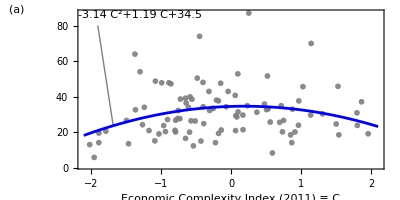
(a)
inventory of main input (days)
-Graphics-

```mathematica
Module[{dataset,font="Arial",fontSize=11,sty,imageSize={8.7*72/2.54(**3.42/3.55*)},aspectRatio=.5,horizontalRange=Sequence[-2.1,2.1],lmf,tickColor=Gray,ticksSty,fitStyle=Directive[Blue,AbsoluteThickness[2]],year=2011,ticksStyle=Directive[Gray,FontFamily->"Times"]},

sty=Style[#,{Black,FontFamily->font,FontSize->fontSize}]&;
ticksSty=Style[#,{FontFamily->font,FontSize->fontSize,tickColor}]&;
dataset=combinedDatasets[Select[#eciValue=!=Missing["Unmatched"]&&Head[#DaysOfInventoryOfMainInput]=!=Missing&]];
Echo[Length[dataset]];
lmf=dataset[LinearModelFit[{#eciValue["SliceData",year]⟦1⟧,QuantityMagnitude@#DaysOfInventoryOfMainInput}&/@#,{x,x^2},x]&];
Echo[lmf];
Echo[lmf["ANOVATable"]];
Echo[Row[{"RSquared: ",lmf["RSquared"],", AdjustedRSquared: ",lmf["AdjustedRSquared"]}]];

Echo[Map[If[NumericQ[#]&&Not[IntegerQ[#]],If[Abs[#]≥10,Round[#,1],Round[#,.01]],#]&,lmf["ECI"],{1,∞}]];

eciFigure=Row[{
Column[{Style[sty@"(a)",Bold],(*"",*)Rotate[Column[sty/@{"inventory of main input (days)"(*,"(days of production)"*)},Spacings->0],90Degree],""(*,""*)},Spacings->0.3,Alignment->{Center,Bottom}]
,
Show[dataset[ListPlot[{{#eciValue["SliceData",2011][[1]],QuantityMagnitude[#DaysOfInventoryOfMainInput]}}&/@#,
PlotMarkers->({Style[CountryData[#Economy,"UNCode"],FontFamily->font],7}&/@#),
PlotStyle->Directive[Gray,Opacity[.7]]
]&]
,Plot[lmf[x],Evaluate@{x,horizontalRange},PlotStyle->fitStyle],
PlotRange->{{horizontalRange},{1,87}},
PlotRangeClipping->False,
Prolog-> {
Inset[Map[If[NumericQ[#]&&Not[IntegerQ[#]],

If[Abs[#]≥10,Round[#,.1],Round[#,.01]]

,#]&,lmf[Style["C",{FontFamily->font}]],{1,∞}],Scaled[{0,1}],{-1.05,1.7}],

{Gray,Line[{{-1.68,lmf[-1.68]},{-1.9,80}}]},


Inset[sty@"(a)",Scaled@{-.2,1}]},
Frame->True,
Axes->None,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->ticksStyle,FrameLabel->({Row[{sty@"Economic Complexity Index (2011)",sty@" ≡ ",Style["C",{FontFamily->font}]}],None}),
ImageSize->imageSize,AspectRatio->aspectRatio]},
Alignment->Bottom]
]
```

```mathematica
Export["test.pdf",%];
```

### panel (b)

#### run simulations of the best response for α=0.1 and several values of β

Import the functions strategiesThatCouldBeBestResponses and probSuccess:

```mathematica
Get["set_strategies_that_could_be_best_response.wl"];
```

```mathematica
Module[{utility(*,β=.4*),α=0.1,strategies,br,probSuccess},
utility[{mInput_,τInput_},FInput_,{αInput_,βInput_}]:=Probability[S≥τInput,S\[Distributed]BinomialDistribution[mInput,FInput]] τInput^βInput-αInput mInput;

bestResponseα0p1=
ParallelTable[
strategies=strategiesThatCouldBeBestResponses[{α,β},F];
br=First[MaximalBy[strategies,utility[#,F,{α,β}]&]];
probSuccess=If[br=!={0,0},Probability[S≥br⟦2⟧,S\[Distributed]BinomialDistribution[br⟦1⟧,F]],0];

<|"α"->α,"β"->β,"F"->F,"bestResponse"->br,"Fdot"-> (probSuccess[br,F] (1+F ("L"-1))-"L" F)*Boole[br[[2]]>0]
|>
,{F,0,1,.1},{β,0.35,0.45,.1}];
]
```

```mathematica
Module[{utility(*,β=.4*),α=0.1,strategies,br,probSuccess},
utility[{mInput_,τInput_},FInput_,{αInput_,βInput_}]:=Probability[S≥τInput,S\[Distributed]BinomialDistribution[mInput,FInput]] τInput^βInput-αInput mInput;

bestResponseα0p1=
ParallelTable[
strategies=strategiesThatCouldBeBestResponses[{α,β},F];
br=First[MaximalBy[strategies,utility[#,F,{α,β}]&]];
probSuccess=If[br=!={0,0},Probability[S≥br⟦2⟧,S\[Distributed]BinomialDistribution[br⟦1⟧,F]],0];

<|"α"->α,"β"->β,"F"->F,"bestResponse"->br,"Fdot"-> (probSuccess[br,F] (1+F ("L"-1))-"L" F)*Boole[br[[2]]>0]
|>
,{F,0,1,.001},{β,0.35,0.45,.01}];
]//AbsoluteTiming
```

{741.978,Null}

```mathematica
bestResponseα0p1>>FileNameJoin[{NotebookDirectory[],"simulated_data","bestResponse_alpha0p1_severalBeta"}];
```

```mathematica
bestResponseα0p1=(<<(FileNameJoin[{NotebookDirectory[],"simulated_data","bestResponse_alpha0p1_severalBeta"}]));
```

#### make figure 6(b)

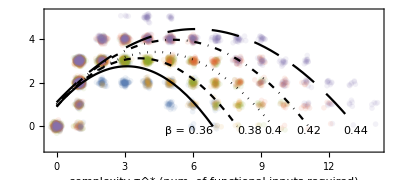
(b)
redundancy m^* - τ^*

-Graphics-

```mathematica
Module[{sty,font="Arial",τredundancy,fit,bestResponseData,colors,plotStyles,curveStyles,ϵ=.008,roundCoefficients,imageSize={8.7 72/2.54(**.95*)(**3.42/3.55*)},aspectRatio=.45,ticksStyle,opacity=.1},

sty=Style[#,{FontFamily->font,FontSize->10}]&;
ticksStyle=Directive[Gray,FontFamily->font];

bestResponseData=Take[Transpose[bestResponseα0p1],{2,-1,2}];

τredundancy=Map[{#bestResponse[[2]],Subtract@@#bestResponse}&,bestResponseData,{2}];
fit=LinearModelFit[#,{τ,τ^2},τ]&/@τredundancy;
(*Print[#["RSquared"]&/@fit];Print[#["ANOVATable"]&/@fit];*)
colors =ColorData[97][#]&/@Range[1,Length[τredundancy]];
plotStyles=Directive[Opacity[opacity],#]&/@colors;
curveStyles={Directive[Black],Directive[Black,Dashed],Directive[Black,Dotted],Directive[Black,DotDashed],Directive[Black,Dashing[{0.05,0.03}]]};
roundCoefficients[expression_,precision_]:=Replace[expression,x_?NumericQ->If[x==IntegerPart[x],IntegerPart[x],Round[x,precision]],{0,∞}];

redundancyFigure=
Column[{

Row[{
Column[{
Style[sty@"(b)",Bold]
(*,""*)
,Rotate[(Style[#,Black])&@sty@"redundancy m^* - τ^*",90Degree]
,"",""
},Spacings->.5],
Spacer[1.5],
Show[
ListPlot[τredundancy+(*RandomReal[{-ϵ,ϵ aspectRatio},Dimensions@τredundancy]*)
RandomVariate[MultinormalDistribution[{0,0},{{ϵ,0},{0,ϵ}}],Most@Dimensions@τredundancy]
,PlotMarkers->●,PlotStyle->plotStyles
,PlotRange->{Automatic,{-1.05,5.25}}],

Plot[Evaluate[((If[#[τ]>0,1,∞]*#[τ]&)/@fit)],{τ,Min[First/@Flatten[#,1]&@τredundancy],Max[First/@Flatten[#,1]&@τredundancy]},PlotStyle->curveStyles],
PlotRangeClipping->False,
AspectRatio->aspectRatio,
Frame->True,
FrameLabel->{(Style[#,Black])&@sty@"complexity τ^* (num. of functional inputs required)",None},
ImageSize->imageSize
,AspectRatio->aspectRatio
,FrameTicksStyle->ticksStyle
,Epilog->{
Inset[

Row[{
(* write "β = " before the 0.36" *)
If[#1==.36,
Framed[sty@"β = "
,FrameStyle->None,FrameMargins->0,RoundingRadius->0,ContentPadding->False]
,""],

Framed[Style[#1,{FontFamily->font,FontSize->10,Black}],Background->Directive[#2,Opacity[.5]],FrameStyle->None,FrameMargins->.5,RoundingRadius->2,ContentPadding->False]},Alignment->Bottom],#3,{0,1.2}+Which[#1==.36,{.5,0},#1==.38,{-.5,0},True,{-.25,0}],Alignment->Center]&@@@Transpose[{#⟦1,"β"⟧&/@bestResponseData,colors,{Max[τ/.Solve[#[τ]==0,τ]],0}&/@fit}]

}
]
},Alignment->{Left,Bottom}]
}
,Alignment->Center,Spacings->0.5]
]
```

#### without confidence bands

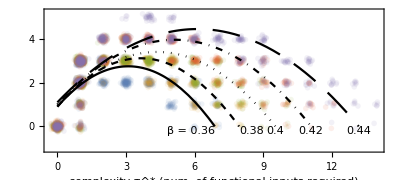
(a)
inventory of main input (days)
-Graphics-
(b)
redundancy m^* - τ^*

-Graphics-

```mathematica
Column[{eciFigure,redundancyFigure},Alignment->Left,Spacings->-.2]
Export[FileNameJoin[{"figures","figure6_withoutMeanPredictionBands.pdf"}],%];
```

p-value of the -3.14 C^2 coefficient: 0.022

The R^2 jumps from 0.008 to 0.063 (and adjusted R^2 jumps from -0.002 to 0.043) when we include C^2 together with {1,C}

### Figure 6: stack figures vertically

#### inventory and ECI figure with confidence bands (MeanPredictionBands at 95% confidence level)

95

FittedModel[34.4829+1.18922 x-3.13635 x^2]

| DF | SS | MS | F-Statistic | P-Value
x | 1 | 156.332 | 156.332 | 0.821005 | 0.367254
x^2 | 1 | 1030.44 | 1030.44 | 5.41152 | 0.0222008
Error | 92 | 17518.2 | 190.415 |  | 
Total | 94 | 18705. |  |  |

RSquared: 0.0634467, AdjustedRSquared: 0.0430868

34+1.19 ECI-3.14 ECI^2

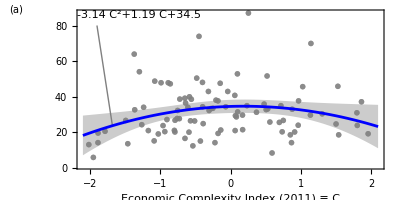
(a)
inventory of main input (days)
-Graphics-

```mathematica
Module[{dataset,font="Arial",fontSize=10,sty,imageSize={8.7*72/2.54(**3.42/3.55*)},aspectRatio=.5,horizontalRange=Sequence[-2.1,2.1],lmf,tickColor=Gray,ticksSty,fitStyle=Directive[Blue,AbsoluteThickness[2]],year=2011,ticksStyle=Directive[Gray,FontFamily->"Times"]},
sty=Style[#,{Black,FontFamily->font,FontSize->fontSize}]&;
ticksSty=Style[#,{FontFamily->font,FontSize->fontSize,tickColor}]&;
dataset=combinedDatasets[Select[#eciValue=!=Missing["Unmatched"]&&Head[#DaysOfInventoryOfMainInput]=!=Missing&]];
Echo[Length[dataset]];
lmf=dataset[LinearModelFit[{#eciValue["SliceData",year]⟦1⟧,QuantityMagnitude@#DaysOfInventoryOfMainInput}&/@#,{x,x^2},x]&];
Echo[lmf];
Echo[lmf["ANOVATable"]];
Echo[Row[{"RSquared: ",lmf["RSquared"],", AdjustedRSquared: ",lmf["AdjustedRSquared"]}]];

Echo[Map[If[NumericQ[#]&&Not[IntegerQ[#]],If[Abs[#]≥10,Round[#,1],Round[#,.01]],#]&,lmf["ECI"],{1,∞}]];

eciFigureConfidenceBands=Row[{
Column[{Style[sty@"(a)",Bold],(*"",*)Rotate[Column[sty/@{"inventory of main input (days)"(*,"(days of production)"*)},Spacings->0],90Degree],""(*,""*)},Spacings->0.3,Alignment->{Center,Bottom}]
,
Show[dataset[ListPlot[{{#eciValue["SliceData",2011][[1]],QuantityMagnitude[#DaysOfInventoryOfMainInput]}}&/@#,
PlotMarkers->({Style[CountryData[#Economy,"UNCode"],FontFamily->font],7}&/@#),
PlotStyle->Directive[Gray,Opacity[.7]]
]&]
,

Plot[Evaluate@Join[{lmf[x]},lmf["MeanPredictionBands",ConfidenceLevel->.95]],Evaluate@{x,horizontalRange},PlotStyle->{fitStyle,None,None,None,None},Filling->{3->{{2},Directive[Gray,Opacity[.4]]}}],
PlotRange->{{horizontalRange},{1,87}},
PlotRangeClipping->False,
Prolog-> {
Inset[Map[If[NumericQ[#]&&Not[IntegerQ[#]],

If[Abs[#]≥10,Round[#,.1],Round[#,.01]]

,#]&,lmf[Style["
StyleBox[\"C\",\nFontSlant->\"Italic\"]",{FontFamily->font}]],{1,∞}],Scaled[{0,1}],{-1.05,1.7}],

{Gray,Line[{{-1.68,lmf[-1.68]},{-1.9,80}}]},


Inset[sty@"(a)",Scaled@{-.2,1}]},
Frame->True,
Axes->None,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicksStyle->ticksStyle,FrameLabel->({Row[{sty@"Economic Complexity Index (2011)",sty@" ≡ ",Style["
StyleBox[\"C\",\nFontSlant->\"Italic\"]",{FontFamily->font}]}],None}),
ImageSize->imageSize,AspectRatio->aspectRatio]},
Alignment->Bottom]
]
```

#### combine them

```mathematica
Column[{eciFigureConfidenceBands,redundancyFigure},Alignment->Left,Spacings->-.4]
Export[FileNameJoin[{"figures","figure6.pdf"}],%];
```

(a)
inventory of main input (days)
-Graphics-
(b)
redundancy m^* - τ^*

-Graphics-